## Primera Parte: Análisis inicial de los datos enpecyt2013_cb1.dbf

```mathematica
data = Import["/Users/guillemontanari/C3/Datos/ENPECyT/2013/enpecyt2013_bd/enpecyt2013_cb1.dbf", "LabeledData"];
```

```mathematica
(* Ver cantidad de columnas / varia en la DB *)
Length[data]
```

245

```mathematica
PositionIndex[data[[All,1]]];
```

```mathematica
(* S3P1 - columna 8 - es el nivel de instruccion: de 0 a 10 *)
Length[data[[8,2]]]
```

2857

```mathematica
(* S4P10 - columna 8 - es el acceso a internet 1 Si - 2 No - Null *)Length[data[[99,2]]]
```

2857

```mathematica
(* FAC - columna 245 - es el nivel de instruccion: de 0 a 10 *)Total[data[[-1,2]]]
```

34818927

## Segunda Parte: Análisis exploratorio

```mathematica
(*Datos 
1 - Nivel de Instruccion Pos 8
2 - Acceso a internet Pos 99 ( 1= SI, 2 = No, NULL ???

Teniendo en cuenta los Factores de expansión Pos 245
*)
```

## Nivel de Instrucción

```mathematica
instruccion = data[[8,2]];
```

```mathematica
factores = data[[-1,2]];
```

```mathematica
datainst= Transpose[{factores, instruccion}];
```

```mathematica
ginstrdata = GatherBy[datainst, #[[2]] & ];
```

```mathematica
datosinstr= ToExpression[Sort[Map[{#[[1,2]],Total[#[[All,1]]] }& ,ginstrdata]]];
```

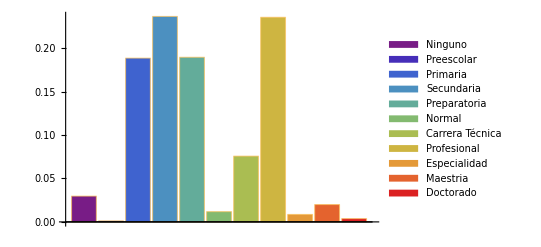

```mathematica
BarChart[N[tdatos[[All,2]]/34818927],ChartStyle->"Rainbow",
ChartLegends->{"Ninguno","Preescolar","Primaria","Secundaria","Preparatoria","Normal","Carrera Técnica","Profesional","Especialidad", "Maestria","Doctorado"}]
```

## Acceso a Internet

```mathematica
internet = data[[99,2]];
```

```mathematica
dataninter = Transpose[{factores, internet}];
```

```mathematica
ginterdata = GatherBy[dataninter, #[[2]] & ];
```

```mathematica
inter =Sort[ToExpression[Map[{#[[1,2]],Total[#[[All,1]]] }& ,ginterdata]]];
```

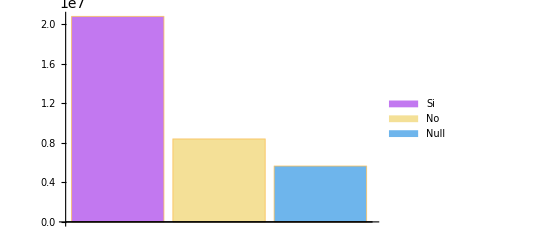

```mathematica
BarChart[inter[[All,2]],ChartStyle->"Pastel",ChartLegends->{"Si","No","Null"}]
```

## Primera Parte: Análisis inicial de los datos enpecyt2013_cs.dbf

```mathematica
data2 = Import["/Users/guillemontanari/C3/Datos/ENPECyT/2013/enpecyt2013_bd/enpecyt2013_cs.dbf", "LabeledData"];
```

```mathematica
Length[data2]
```

23

```mathematica
PositionIndex[data2[[All,1]]];
```

```mathematica
data2[[{10, 11,15,23},1]]
```

{SEX,EDA,NIV,FAC18}

```mathematica
Length[data2[[23,2]]]
```

10418

```mathematica
Total[data2[[-1,2]]]
```

34818927

## Segunda Parte: Análisis inicial de los datos Sexo

```mathematica
sexo= data2[[10,2]];
```

```mathematica
factores2 = data2[[-1,2]];
```

```mathematica
datan2 = Transpose[{factores2, sexo}];
```

```mathematica
gdata2 = GatherBy[datan2, #[[2]] & ];
```

```mathematica
datos2 = Map[Total[#[[All,1]]] & ,gdata2]
```

{18644082,16174845}

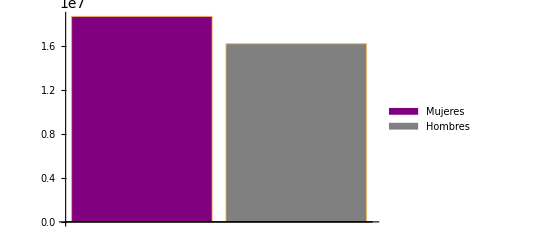

```mathematica
BarChart[datos2,ChartStyle->{Purple,Gray},ChartLegends->{"Mujeres", "Hombres"}]
```

## Edad

```mathematica
edad = data2[[11,2]];
```

```mathematica
edata = Transpose[{factores2, edad}]
```

{{0,067},{0,054},{0,059},{0,009},{0,011},{14315,032},{0,030},{0,062},{0,004},{0,005},{4772,027},{9543,071},{0,061},{0,010},{0,011},{0,038},{9151,034},{0,002},10382,{12771,019},{0,064},{6660,047},{0,000},{0,013},{0,017},{0,038},{8970,050},{0,008},{0,011},{0,017},{4485,055},{0,010},{0,001},{0,052},{0,016},{8970,021},{4503,041}}
 |  |  |  |

```mathematica
Quotient[ToExpression[edata[[-1,2]]],10]
```

4

```mathematica
edadf= GatherBy[edata,Quotient[ToExpression[#[[2]]],10]&]
```

{1}
 |  |  |  |

```mathematica
Length[edadf]
```

11

```mathematica
tedad= Sort[Map[{Quotient[ToExpression[#[[1,2]]],10],Total[#[[All,1]]]}&,edadf]]
```

{{0,0},{1,1844188},{2,8258189},{3,7585995},{4,7007222},{5,5122807},{6,3029809},{7,1416874},{8,520109},{9,33734},{10,0}}

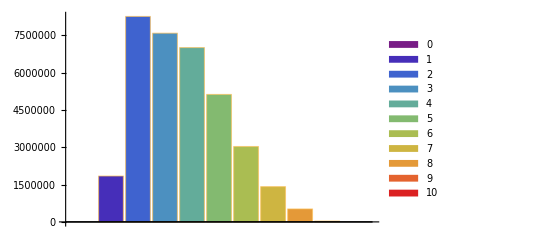

```mathematica
BarChart[tedad[[All,2]], ChartStyle->"Rainbow", ChartLegends->{tedad[[All,1]]}]
```